## 3rd Assignment: Stochastic FEM F. I. Giasemis

### KL expansion

#### Parameters from the problem

```mathematica
b=3;
a=2;
M=8; (* Number of terms in the KL expansion. *)
R=5000; (* Number of realizations. *)
```

#### Eigenvalues and eigenfunctions for f(x)

```mathematica
For[n=0,n<M/2,n=n+1;
sol=NSolve[{1/b -x Tan[x a]==0,(n-1) Pi/a≤x≤(n-1/2) Pi/a},x];
wodd[n]=Part[x/.sol,1];
λodd[n]=2b/(1+wodd[n]^2 b^2);
codd[n]=1/Sqrt[a+Sin[2 wodd[n] a]/(2 wodd[n])];
φodd[n][x_]:=codd[n] Cos[wodd [n]x];

sol=NSolve[{1/b Tan[x a]+x==0,(n-1/2) Pi/a≤x≤(n) Pi/a},x];
weven[n]=Part[x/.sol,1];
λeven[n]=2b/(1+weven[n]^2 b^2);
ceven[n]=1/Sqrt[a-Sin[2 weven[n] a]/(2 weven[n])];
φeven[n][x_]:=ceven[n] Sin[weven[n] x]
]
```

#### Random variables ξ(θ)

```mathematica
For[i=0,i<R,i=i+1;
ξ[i]=RandomVariate[NormalDistribution[],M]
]
```

#### Realization of f(x) and E(x)

```mathematica
RealizationF[i_,x_]:=Sum[Sqrt[λodd[n]]φodd[n][x-2]ξ[i][[n]],{n,1,M/2}]+Sum[Sqrt[λeven[n]]φeven[n][x-2.5]ξ[i][[M/2+n]],{n,1,M/2}];
Realization[i_,x_]:=10^5(1+0.1 RealizationF[i,x]);
```

#### Example plot of a realization of E(x)

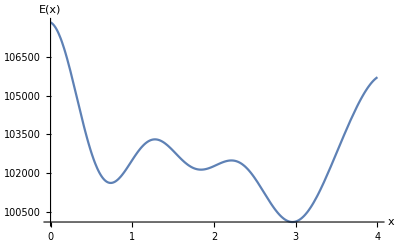

```mathematica
Plot[Realization[567,x],{x,0,4},AxesLabel->{"x","E(x)"}]
```

#### Ensemble averages and variances

```mathematica
EnsembleAverage[x_]:=Mean[Table[Realization[i,x],{i,1,R}]]
EnsembleVariance[x_]:=Variance[Table[Realization[i,x],{i,1,R}]]
```

#### Example calculation of ensemble average and variance

```mathematica
EnsembleAverage[2]
EnsembleVariance[2]
```

100125.

1.09113×10^8

#### Plot of 10 realizations

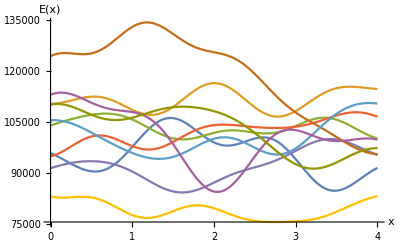

```mathematica
list={};
For[i=0,i<10,i=i+1;
AppendTo[list,Realization[i,x]]
]
Plot[list,{x,0,4},AxesLabel->{"x","E(x)"}]
```

#### Plot of 10 realizations

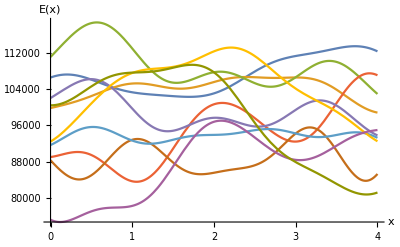

```mathematica
list={};
For[i=4300,i<4310,i=i+1;
AppendTo[list,Realization[i,x]]
]
Plot[list,{x,0,4},AxesLabel->{"x","E(x)"}]
```

### Stochastic FEM

#### The stiffness matrix for one element

```mathematica
aelem=0.05;
belem=0.05;
ν=0.3;
t=0.2;
r=aelem/belem;
ρ=(1-ν)/2;
μ=3(1+ν)/2;
λ=3(1-3ν)/2;

kinput=t /(12(1-ν^2)){{4/r+4 ρ r,0,0,0,0,0,0,0},{μ,4r+4ρ/r,0,0,0,0,0,0},{-4/r+2 ρ r,λ,4/r+4 ρ r,0,0,0,0,0},{-λ,2r-4ρ/r,-μ,4r+4ρ/r,0,0,0,0},{-2/r-2ρ r,-μ,2/r-4ρ r,λ,4/r+4ρ r,0,0,0},{-μ,-2r-2ρ/r,-λ,-4r+2ρ/r,μ,4r+4ρ/r,0,0},{2/r-4ρ r,-λ,-2/r-2 ρ r,μ,-4/r+2 ρ r,λ,4/r+4 ρ r,0},{λ,-4r+2ρ/r,μ,-2r-2ρ/r,-λ,2r-4ρ/r,-μ,4r+4ρ/r}};
k=kinput+Transpose[kinput]-DiagonalMatrix[{kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]]}];

klocal[x_]:=(
EY=f[x];
Return[EY k])
```

#### Assembling the global stiffness matrix

```mathematica
dim=(40+1) (10+1) 2;
global[i_,j_,m_,n_]:=(
x=Mod[i,41] 2aelem-aelem;
kglobal=ConstantArray[0,{dim,dim}];
kglobal[[2 i-1,2 i-1]]+=klocal[x][[1,1]];
kglobal[[2 i-1,2 i]]+=klocal[x][[1,2]];
kglobal[[2 i-1,2 j-1]]+=klocal[x][[1,3]];
kglobal[[2 i-1,2 j]]+=klocal[x][[1,4]];
kglobal[[2 i-1,2 m-1]]+=klocal[x][[1,5]];
kglobal[[2 i-1,2 m]]+=klocal[x][[1,6]];
kglobal[[2 i-1,2 n-1]]+=klocal[x][[1,7]];
kglobal[[2 i-1,2 n]]+=klocal[x][[1,8]];
kglobal[[2 i,2 i-1]]+=klocal[x][[2,1]];
kglobal[[2 i,2 i]]+=klocal[x][[2,2]];
kglobal[[2 i,2 j-1]]+=klocal[x][[2,3]];
kglobal[[2 i,2 j]]+=klocal[x][[2,4]];
kglobal[[2 i,2 m-1]]+=klocal[x][[2,5]];
kglobal[[2 i,2 m]]+=klocal[x][[2,6]];
kglobal[[2 i,2 n-1]]+=klocal[x][[2,7]];
kglobal[[2 i,2 n]]+=klocal[x][[2,8]];
kglobal[[2 j-1,2 i-1]]+=klocal[x][[3,1]];
kglobal[[2 j-1,2 i]]+=klocal[x][[3,2]];
kglobal[[2 j-1,2 j-1]]+=klocal[x][[3,3]];
kglobal[[2 j-1,2 j]]+=klocal[x][[3,4]];
kglobal[[2 j-1,2 m-1]]+=klocal[x][[3,5]];
kglobal[[2 j-1,2 m]]+=klocal[x][[3,6]];
kglobal[[2 j-1,2 n-1]]+=klocal[x][[3,7]];
kglobal[[2 j-1,2 n]]+=klocal[x][[3,8]];
kglobal[[2 j,2 i-1]]+=klocal[x][[4,1]];
kglobal[[2 j,2 i]]+=klocal[x][[4,2]];
kglobal[[2 j,2 j-1]]+=klocal[x][[4,3]];
kglobal[[2 j,2 j]]+=klocal[x][[4,4]];
kglobal[[2 j,2 m-1]]+=klocal[x][[4,5]];
kglobal[[2 j,2 m]]+=klocal[x][[4,6]];
kglobal[[2 j,2 n-1]]+=klocal[x][[4,7]];
kglobal[[2 j,2 n]]+=klocal[x][[4,8]];
kglobal[[2 m-1,2 i-1]]+=klocal[x][[5,1]];
kglobal[[2 m-1,2 i]]+=klocal[x][[5,2]];
kglobal[[2 m-1,2 j-1]]+=klocal[x][[5,3]];
kglobal[[2 m-1,2 j]]+=klocal[x][[5,4]];
kglobal[[2 m-1,2 m-1]]+=klocal[x][[5,5]];
kglobal[[2 m-1,2 m]]+=klocal[x][[5,6]];
kglobal[[2 m-1,2 n-1]]+=klocal[x][[5,7]];
kglobal[[2 m-1,2 n]]+=klocal[x][[5,8]];
kglobal[[2 m,2 i-1]]+=klocal[x][[6,1]];
kglobal[[2 m,2 i]]+=klocal[x][[6,2]];
kglobal[[2 m,2 j-1]]+=klocal[x][[6,3]];
kglobal[[2 m,2 j]]+=klocal[x][[6,4]];
kglobal[[2 m,2 m-1]]+=klocal[x][[6,5]];
kglobal[[2 m,2 m]]+=klocal[x][[6,6]];
kglobal[[2 m,2 n-1]]+=klocal[x][[6,7]];
kglobal[[2 m,2 n]]+=klocal[x][[6,8]];
kglobal[[2 n-1,2 i-1]]+=klocal[x][[7,1]];
kglobal[[2 n-1,2 i]]+=klocal[x][[7,2]];
kglobal[[2 n-1,2 j-1]]+=klocal[x][[7,3]];
kglobal[[2 n-1,2 j]]+=klocal[x][[7,4]];
kglobal[[2 n-1,2 m-1]]+=klocal[x][[7,5]];
kglobal[[2 n-1,2 m]]+=klocal[x][[7,6]];
kglobal[[2 n-1,2 n-1]]+=klocal[x][[7,7]];
kglobal[[2 n-1,2 n]]+=klocal[x][[7,8]];
kglobal[[2 n,2 i-1]]+=klocal[x][[8,1]];
kglobal[[2 n,2 i]]+=klocal[x][[8,2]];
kglobal[[2 n,2 j-1]]+=klocal[x][[8,3]];
kglobal[[2 n,2 j]]+=klocal[x][[8,4]];
kglobal[[2 n,2 m-1]]+=klocal[x][[8,5]];
kglobal[[2 n,2 m]]+=klocal[x][[8,6]];
kglobal[[2 n,2 n-1]]+=klocal[x][[8,7]];
kglobal[[2 n,2 n]]+=klocal[x][[8,8]];
Return[kglobal])
```

#### The global stiffness matrix

```mathematica
Kglobal:=(
Kglobal= ConstantArray[0,{dim,dim}];
For[index =0,index≤408,index+=1,
i=1+index;
j=2+index;
m=43+index;
n=42+index;
If[Divisible[i,41]==False, Kglobal+=global[i,j,m,n]]
];
Return[Kglobal])
```

#### Boundary conditions

```mathematica
fix[x_]:=(
For[i=1,i≤dim,i+=1,
KGLOBAL[[x,i]]=0;
KGLOBAL[[i,x]]=0;];
KGLOBAL[[x,x]]=10^10;)
```

```mathematica
fixall:=(
For[x=1,x≤821,x+=82,
fix[x]];
For[x=2,x≤822,x+=82,
fix[x]];)
```

#### External forces

```mathematica
F=ConstantArray[0,dim];
P= RandomVariate[NormalDistribution[10,2],1];
F[[dim]] = -P[[1]];
```

#### Solve the system

```mathematica
U[R_]:=(
F=ConstantArray[0,dim];
P= RandomVariate[NormalDistribution[10,2],1];
F[[dim]] = -P[[1]];

f[x_]:=Realization[R,x];

KGLOBAL=Kglobal;

fixall;

sol=Inverse[KGLOBAL].F;

Return[sol];)
```

#### Histogram of response u

```mathematica
CalculationTime=Timing[Quiet[u=Table[-U[real][[82]],{real,1,5000}];]][[1]]
```

686.

```mathematica
Export["response_data.txt",u,"CSV"]
```

response_data.txt

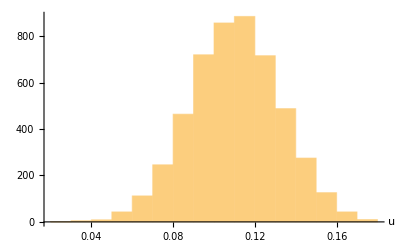

```mathematica
Histogram[u,{0.01},AxesLabel->{"u",""}]
```

#### Empirical pdf

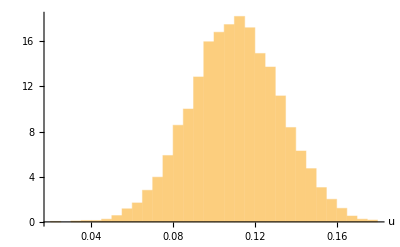

```mathematica
Histogram[u,{0.005},"PDF",AxesLabel->{"u",""}]
```

### Principal Component Analysis

#### Principal Components

```mathematica
Quiet[V=Table[U[real],{real,1,100}]];
```

```mathematica
Dimensions[V]
```

{100,902}

```mathematica
Dimensions[Transpose[V].V]
```

{902,902}

```mathematica
{vals,vecs}=Eigensystem[Transpose[V].V];
```

```mathematica
Φ={};
For[l=1,l≤dim,l++,
If[vals[[l]]>10^-15,AppendTo[Φ,vecs[[l]]]]];
Φ=Transpose[Φ];
```

```mathematica
Dimensions[KGLOBAL]
Dimensions[F]
```

{902,902}

{902}

```mathematica
Dimensions[Transpose[Φ].KGLOBAL.Φ]
Dimensions[Transpose[Φ].F]
```

{15,15}

{15}

#### Solve the system

```mathematica
Upca[R_]:=(
F=ConstantArray[0,dim];
P= RandomVariate[NormalDistribution[10,2],1];
F[[dim]] = -P[[1]];

f[x_]:=Realization[R,x];

KGLOBAL=Kglobal;

fixall;

Kred =Transpose[Φ].KGLOBAL.Φ;
Fred = Transpose[Φ].F;

sol=Inverse[Kred].Fred;

Return[Φ.sol];)
```

#### Histogram of response u

```mathematica
CalculationTime=Timing[Quiet[upca=Table[-Upca[real][[82]],{real,1,5000}];]][[1]]
```

331.359

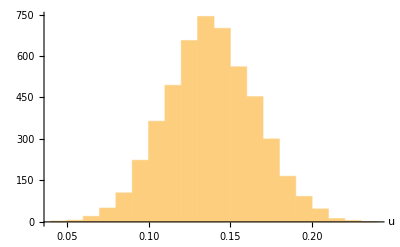

```mathematica
Histogram[upca,{0.01},AxesLabel->{"u",""}]
```

#### Empirical pdf

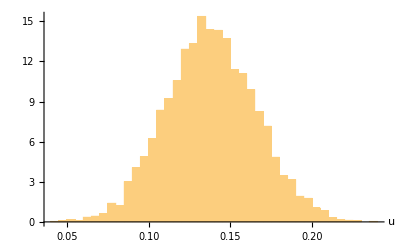

```mathematica
Histogram[upca,{0.005},"PDF",AxesLabel->{"u",""}]
```

#### Comparison of pdfs

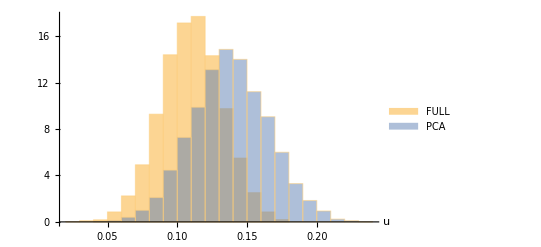

```mathematica
Histogram[{u,upca},{0.01},"PDF",ChartLegends->{"FULL","PCA"},AxesLabel->{"u"}]
```